## init

Set the library’s directory first!

```mathematica
directory="/home/tchr/Projects/Mathematica/MSE-Mathematica/";
Get["mse.m",Path->directory];
```

## Import precomputed data

Set the data’s directory preferably in the variable ‘filename’.

```mathematica
filename=directory<>"import/"<>"round1m1-1.xls.pre.dat";
```

Load the data in variables with meaningful names

```mathematica
import[filename,"precomp"];
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}
```

{{Market,Upstream,DownStream,Distance1,Distance2,Distance3,Match},6,{{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50}},{{30},{25},{17},{6},{16},{27},{45},{23},{46},{8},{41},{21},{44},{38},{18},{11},{35},{42},{24},{15},{28},{43},{14},{9},{29},{10},{32},{26},{19},{34},{12},{1},{49},{39},{4},{5},{37},{7},{40},{33},{31},{2},{20},{3},{22},{50},{36},{48},{47},{13}}},23,{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},10,{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50}},1}}}
 |  |  |  |

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
payoffMatrix=CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
ineqmembers=Cineqmembers[mate];
```

```mathematica
dataArray=CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

```mathematica
seedrandom=4321;
```

The global variable “permuteinvariant” when set to true the order of the attributes is set related to their statistics.

```mathematica
permuteinvariant=True;
```

### Differential Evolution Method

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution",permuteinvariant_:False,printflag_:False] is MSE specific and uses the optimize function. It uses objective function (that counts the number of satisfied inequalities). It returns a list {max,{x1->value1, x2->value2, ...}} where max is the maximum number of satisfied inequalities found and the solution {x1,x2,...}

```mathematica
method1={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->seedrandom,"ScalingFactor"->0.6,"SearchPoints"->Automatic,"Tolerance"->0.001};
sol1=maximize[dataArray,noAttr,method1,permuteinvariant,True];
```

The new ordering of attributes used for calculating the solutio order={2,1}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 4321, ScalingFactor -> 0.6, SearchPoints -> Automatic, Tolerance -> 0.001}

Completed : {29966.,{Distance2→3.83928,Distance3→2.93331}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1200 | 1189 | 1205 | 1205 | 1199 | 1197 | 1207 | 1198 | 1198 | 1191 | 1202 | 1201 | 1198 | 1209 | 1197 | 1206 | 1195 | 1196 | 1188 | 1201 | 1187 | 1205 | 1198 | 1203 | 1191
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 98 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

### Particle Swarm Optimization

```mathematica
?pso
```

pso[objFun_,nparts_Integer,bndLo_List,bndUp_List,niter_Integer:100,r_Integer:1]
nparts: the number of particles
bndLo: a list of the lower bounds, one for each dimension
bndUp: a list of the upper bounds, one for each dimension
niter: Number of iterations
r: length of the toroidal neighbour scheme e.g. r=1 gives (i-1 mod nparts, i, i+1 mod nparts) as the neighbours of particle i

```mathematica
method2={"ParticleSwarmOptimization","nparts"->32,"bndLo"->-10,"bndUp"->10,"niter"->200,"r"->1,"RandomSeed"->seedrandom};
sol2=maximize[dataArray,noAttr,method2,permuteinvariant,True];
```

The new ordering of attributes used for calculating the solutio order={2,1}

Method {ParticleSwarmOptimization, nparts -> 32, bndLo -> -10, bndUp -> 10, niter -> 200, r -> 1, RandomSeed -> 4321}

Completed : {29964,{Distance2→3.70796,Distance3→2.69361}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1201 | 1190 | 1206 | 1205 | 1199 | 1198 | 1207 | 1196 | 1197 | 1191 | 1202 | 1200 | 1197 | 1209 | 1196 | 1206 | 1194 | 1195 | 1190 | 1199 | 1186 | 1205 | 1198 | 1204 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

## Confidence Intervals

```mathematica
sol=sol1;method=method1;
(*sol=sol2;method=method2;*)
```

```mathematica
ssSize=3;numSubsamples=50;alpha=0.05;
```

Starting pointIdentified process where alpha = 0.05

{10, 23, 25} {8, 20, 21} {11, 15, 21} {14, 17, 23} {6, 7, 14} {5, 6, 22} {5, 8, 14} {5, 19, 20} {8, 14, 19} {5, 7, 8}
Iterations completed:10
 {10, 17, 19} {3, 16, 25} {5, 10, 16} {13, 19, 24} {4, 13, 15} {4, 6, 13} {13, 15, 21} {7, 14, 17} {10, 11, 21} {3, 7, 14}
Iterations completed:20
 {13, 15, 21} {9, 18, 19} {3, 16, 20} {17, 19, 22} {11, 21, 25} {4, 15, 25} {1, 18, 23} {7, 12, 16} {6, 17, 23} {8, 22, 25}
Iterations completed:30
 {7, 17, 24} {4, 14, 21} {1, 7, 23} {7, 10, 21} {3, 17, 25} {5, 15, 20} {8, 9, 20} {5, 10, 16} {8, 9, 16} {13, 18, 23}
Iterations completed:40
 {5, 15, 16} {4, 19, 25} {8, 13, 23} {4, 13, 21} {15, 18, 25} {2, 21, 24} {11, 19, 23} {3, 12, 24} {4, 15, 19} {7, 15, 16}
Iterations completed:50

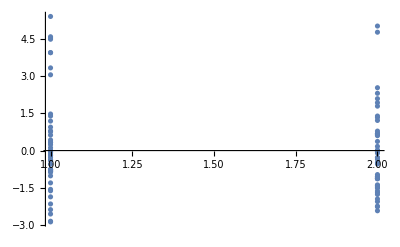
{25.1974,{{{{Symmetric case,{Distance2→{2.28898,5.38957},Distance3→{2.06803,3.7986}}},{Asymmetric case,{Distance2→{2.27235,4.81168},Distance3→{1.3038,3.70668}}}},{{0.75791,-0.00868475},{1.47224,2.30543},{4.58173,5.01258},{-0.832931,0.682947},{-0.00520803,-1.3812},{4.53309,-1.48093},{5.39812,0.168665},{0.325981,1.92675},{0.426178,-1.69417},{3.32807,-1.76548},{-0.805993,1.21268},{-2.84332,-1.6287},{3.94147,-0.00720982},{-0.551375,-1.43314},{1.18699,2.53011},{-0.861914,-1.08195},{-0.771342,-1.12467},{-0.829023,0.670905},{1.39045,-0.540931},{-1.86295,-1.94715},{-0.771342,-1.12467},{0.335783,1.39045},{-0.184586,1.32734},{-1.30053,-1.13807},{-1.61877,-0.966004},{-2.37767,-0.277172},{0.622994,0.675938},{0.112138,0.0204886},{-1.0184,-0.479748},{-0.188845,-2.23771},{-0.783956,-1.51241},{-2.14835,-1.0456},{-0.396,-0.293024},{-0.0878344,-1.40843},{-2.55309,-1.04456},{3.04974,4.76472},{0.94362,1.78797},{3.94147,-0.00720982},{0.236012,0.367657},{-0.273942,0.599996},{4.4806,-0.101724},{-2.87076,-2.05351},{-0.0347719,-0.0437787},{-0.760209,-1.11212},{-0.0883679,0.636256},{-0.854327,-2.26134},{-0.36598,-0.351459},{-1.56174,-2.42369},{0.793133,2.08891},{-0.0182749,0.784402}}},-Graphics-}}

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,permuteinvariant,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
```